increasing accuracy automatically

```mathematica
Clear[W,K,v,V,t,x,T,X];
Clear[w0,A,a,B,b,Λ];
Clear[Kmat,Kinv];

Clear[zero];
zero[x_]=0;

W=w0-A Exp[-a T]+B  X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};


Clear[valA,vala,valB,valw0,ac];
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
valA=1;
vala=4Pi^2;
valB=Exp[-4Pi^2];
veqntemp=V/.ReX->Sqrt[3]-1;
vteqntemp=FullSimplify@ComplexExpand[D[veqntemp,ReT]];
ac=1;
doinit=2.10;

list={{"accuracy","w_0","<T>","V|_0"}};

cnt=0;

While[ac<=100,
ac=ac+1;
Do[
cnt=cnt+1;
valw0=SetPrecision[(doinit+j*10^(-ac))*10^(-18),ac+10];
veqn=veqntemp*10^(46)/.{A->valA,a->vala,B->valB,w0->valw0};
vteqn=vteqntemp/.{A->valA,a->vala,B->valB,w0->valw0};
solvteq=NSolve[vteqn==0,{ReT},Reals,WorkingPrecision->10000];
Clear[relist];
relist={};
Do[
ret=ReT/.solvteq[[i]];
If[ret>0,
relist=Append[relist,ret];,relist=Append[relist,Null]];
,{i,1,Length[solvteq]}];
relist=DeleteCases[relist,Null];
minv=Min[Table[veqn/.ReT->relist[[k]],{k,1,Length[relist]}]];
If[minv<0,Break[];];
listveqn=Table[veqn/.ReT->relist[[k]],{k,1,Length[relist]}];
minvtrue=Min[listveqn];
ret=relist[[Position[listveqn,minvtrue][[1]]]];
,{j,0,10,1}];

doinit=valw0*10^(18)-10^(-ac);
list=Append[list,{ac,doinit*10^(-18),ret,minvtrue*10^(-46)}]
];

Print[N[list]//MatrixForm];
aclist=Table[list[[i,1]],{i,2,Length[list]}];
vminloglist=Table[Log10[list[[i,4]]*10^(-46)],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],vminloglist[[k]]},{k,1,Length[list]-1}]]];
```

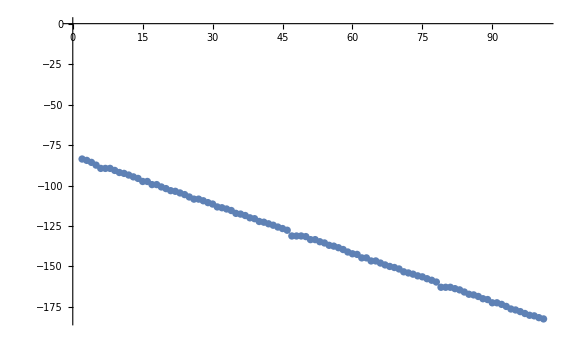
("accuracy" | "w_0" | "<T>" | "V|_0"
2. | 2.16×10^-18 | 1.17457 | 2.33923×10^-38
3. | 2.165×10^-18 | 1.17457 | 3.40413×10^-39
4. | 2.1658×10^-18 | 1.17457 | 2.04061×10^-40
5. | 2.16585×10^-18 | 1.17457 | 4.03858×10^-42
6. | 2.16585×10^-18 | 1.17457 | 3.81155×10^-44
7. | 2.16585×10^-18 | 1.17457 | 3.81155×10^-44
8. | 2.16585×10^-18 | 1.17457 | 3.81155×10^-44
9. | 2.16585×10^-18 | 1.17457 | 2.11127×10^-45
10. | 2.16585×10^-18 | 1.17457 | 1.11037×10^-46
11. | 2.16585×10^-18 | 1.17457 | 3.1028×10^-47
12. | 2.16585×10^-18 | 1.17457 | 3.02468×10^-48
13. | 2.16585×10^-18 | 1.17457 | 2.2435×10^-49
14. | 2.16585×10^-18 | 1.17457 | 2.43266×10^-50
15. | 2.16585×10^-18 | 1.17457 | 3.23771×10^-52
16. | 2.16585×10^-18 | 1.17457 | 3.23771×10^-52
17. | 2.16585×10^-18 | 1.17457 | 3.7331×10^-54
18. | 2.16585×10^-18 | 1.17457 | 3.7331×10^-54
19. | 2.16585×10^-18 | 1.17457 | 1.32682×10^-55
20. | 2.16585×10^-18 | 1.17457 | 1.2668×10^-56
21. | 2.16585×10^-18 | 1.17457 | 6.66562×10^-58
22. | 2.16585×10^-18 | 1.17457 | 2.66515×10^-58
23. | 2.16585×10^-18 | 1.17457 | 2.64871×10^-59
24. | 2.16585×10^-18 | 1.17457 | 2.48428×10^-60
25. | 2.16585×10^-18 | 1.17457 | 8.39975×10^-62
26. | 2.16585×10^-18 | 1.17457 | 3.98813×10^-63
27. | 2.16585×10^-18 | 1.17457 | 3.98813×10^-63
28. | 2.16585×10^-18 | 1.17457 | 3.87705×10^-64
29. | 2.16585×10^-18 | 1.17457 | 2.76624×10^-65
30. | 2.16585×10^-18 | 1.17457 | 3.6596×10^-66
31. | 2.16585×10^-18 | 1.17457 | 5.91732×10^-68
32. | 2.16585×10^-18 | 1.17457 | 1.91685×10^-68
33. | 2.16585×10^-18 | 1.17457 | 3.16666×10^-69
34. | 2.16585×10^-18 | 1.17457 | 3.66334×10^-70
35. | 2.16585×10^-18 | 1.17457 | 6.292×10^-72
36. | 2.16585×10^-18 | 1.17457 | 2.29153×10^-72
37. | 2.16585×10^-18 | 1.17457 | 2.91296×10^-73
38. | 2.16585×10^-18 | 1.17457 | 1.12636×10^-74
39. | 2.16585×10^-18 | 1.17457 | 3.26269×10^-75
40. | 2.16585×10^-18 | 1.17457 | 6.231×10^-77
41. | 2.16585×10^-18 | 1.17457 | 2.23053×10^-77
42. | 2.16585×10^-18 | 1.17457 | 2.30291×10^-78
43. | 2.16585×10^-18 | 1.17457 | 3.02676×10^-79
44. | 2.16585×10^-18 | 1.17457 | 2.26427×10^-80
45. | 2.16585×10^-18 | 1.17457 | 2.64038×10^-81
46. | 2.16585×10^-18 | 1.17457 | 2.40097×10^-82
47. | 2.16585×10^-18 | 1.17457 | 6.83873×10^-86
48. | 2.16585×10^-18 | 1.17457 | 6.83873×10^-86
49. | 2.16585×10^-18 | 1.17457 | 6.83873×10^-86
50. | 2.16585×10^-18 | 1.17457 | 2.83826×10^-86
51. | 2.16585×10^-18 | 1.17457 | 3.7936×10^-88
52. | 2.16585×10^-18 | 1.17457 | 3.7936×10^-88
53. | 2.16585×10^-18 | 1.17457 | 1.93182×10^-89
54. | 2.16585×10^-18 | 1.17457 | 3.31628×10^-90
55. | 2.16585×10^-18 | 1.17457 | 1.15902×10^-91
56. | 2.16585×10^-18 | 1.17457 | 3.58929×10^-92
57. | 2.16585×10^-18 | 1.17457 | 3.88914×10^-93
58. | 2.16585×10^-18 | 1.17457 | 2.88716×10^-94
59. | 2.16585×10^-18 | 1.17457 | 8.68304×10^-96
60. | 2.16585×10^-18 | 1.17457 | 6.82105×10^-97
61. | 2.16585×10^-18 | 1.17457 | 2.82058×10^-97
62. | 2.16585×10^-18 | 1.17457 | 2.02553×10^-99
63. | 2.16585×10^-18 | 1.17457 | 2.02553×10^-99
64. | 2.16585×10^-18 | 1.17457 | 2.52933×10^-101
65. | 2.16585×10^-18 | 1.17457 | 2.52933×10^-101
66. | 2.16585×10^-18 | 1.17457 | 1.29044×10^-102
67. | 2.16585×10^-18 | 1.17457 | 9.02956×10^-104
68. | 2.16585×10^-18 | 1.17457 | 1.02862×10^-104
69. | 2.16585×10^-18 | 1.17457 | 2.28524×10^-105
70. | 2.16585×10^-18 | 1.17457 | 2.85009×10^-106
71. | 2.16585×10^-18 | 1.17457 | 4.97645×10^-108
72. | 2.16585×10^-18 | 1.17457 | 9.75985×10^-109
73. | 2.16585×10^-18 | 1.17457 | 1.75891×10^-109
74. | 2.16585×10^-18 | 1.17457 | 1.58723×10^-110
75. | 2.16585×10^-18 | 1.17457 | 3.87086×10^-111
76. | 2.16585×10^-18 | 1.17457 | 2.70433×10^-112
77. | 2.16585×10^-18 | 1.17457 | 3.0405×10^-113
78. | 2.16585×10^-18 | 1.17457 | 2.40168×10^-114
79. | 2.16585×10^-18 | 1.17457 | 1.39383×10^-117
80. | 2.16585×10^-18 | 1.17457 | 1.39383×10^-117
81. | 2.16585×10^-18 | 1.17457 | 1.39383×10^-117
82. | 2.16585×10^-18 | 1.17457 | 1.9369×10^-118
83. | 2.16585×10^-18 | 1.17457 | 3.36709×10^-119
84. | 2.16585×10^-18 | 1.17457 | 1.66711×10^-120
85. | 2.16585×10^-18 | 1.17457 | 6.69242×10^-122
86. | 2.16585×10^-18 | 1.17457 | 2.69195×10^-122
87. | 2.16585×10^-18 | 1.17457 | 2.9167×10^-123
88. | 2.16585×10^-18 | 1.17457 | 1.16372×10^-124
89. | 2.16585×10^-18 | 1.17457 | 3.63623×10^-125
90. | 2.16585×10^-18 | 1.17457 | 3.58095×10^-127
91. | 2.16585×10^-18 | 1.17457 | 3.58095×10^-127
92. | 2.16585×10^-18 | 1.17457 | 3.80578×10^-128
93. | 2.16585×10^-18 | 1.17457 | 2.05353×10^-129
94. | 2.16585×10^-18 | 1.17457 | 5.32933×10^-131
95. | 2.16585×10^-18 | 1.17457 | 1.32886×10^-131
96. | 2.16585×10^-18 | 1.17457 | 1.28719×10^-132
97. | 2.16585×10^-18 | 1.17457 | 8.70494×10^-134
98. | 2.16585×10^-18 | 1.17457 | 7.03999×10^-135
99. | 2.16585×10^-18 | 1.17457 | 3.03952×10^-135
100. | 2.16585×10^-18 | 1.17457 | 2.3919×10^-136
101. | 2.16585×10^-18 | 1.17457 | 3.91666×10^-137)
-Graphics-

Evaluate both T & X

```mathematica
Clear[W,K,v,V,t,x,T,X];
Clear[w0,A,a,B,b,Λ];
Clear[Kmat,Kinv];

Clear[zero];
zero[x_]=0;

W=w0-A Exp[-a T]+B  X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};
```

(accuracy | w_0 | <T> | <X> | V|_0
2. | 2.16×10^-18 | 1.08584 | 0.714977 | 1.39848×10^-38
3. | 2.163×10^-18 | 1.08588 | 0.714339 | 2.31161×10^-39
4. | 2.1635×10^-18 | 1.08588 | 0.714296 | 3.64801×10^-40
5. | 2.16359×10^-18 | 1.08588 | 0.714296 | 1.43378×10^-41
6. | 2.16359×10^-18 | 1.08588 | 0.714295 | 2.65544×10^-42
7. | 2.16359×10^-18 | 1.08588 | 0.714295 | 3.18978×10^-43
8. | 2.16359×10^-18 | 1.08588 | 0.714295 | 7.44954×10^-45
9. | 2.16359×10^-18 | 1.08588 | 0.714295 | 3.55545×10^-45
10. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.07356×10^-47
11. | 2.16359×10^-18 | 1.08588 | 0.714295 | 1.18052×10^-47
12. | 2.16359×10^-18 | 1.08588 | 0.714295 | 1.08936×10^-49
13. | 2.16359×10^-18 | 1.08588 | 0.714295 | 1.08936×10^-49
14. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.73348×10^-51
15. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.73348×10^-51
16. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.73348×10^-51
17. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.73348×10^-51
18. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.73348×10^-51
19. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.73348×10^-51
20. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.73348×10^-51
21. | 2.16359×10^-18 | 1.08588 | 0.714295 | 5.73348×10^-51)

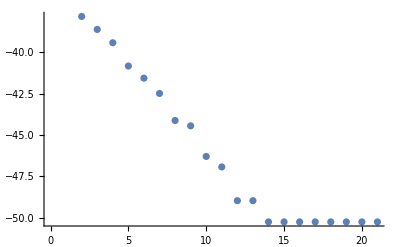

```mathematica
Clear[valA,vala,valB,valw0];

V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
valA=1;
vala=4Pi^2;
valB=Exp[-4Pi^2];
veqntemp=V;

ac=1;
doinit=2.10;

list={{"accuracy","w_0","<T>","<X>","V|_0"}};

cnt=0;

While[ac<=20,
ac=ac+1;
Do[
cnt=cnt+1;
valw0=SetPrecision[(doinit+j*10^(-ac))*10^(-18),ac+10];
veqn=veqntemp*10^(50)/.{A->valA,a->vala,B->valB,w0->valw0};

Quiet[
Block[{$MaxExtraPrecision=∞},
solmin=FindMinimum[veqn,{{ReT,1.0},{ReX,1.0}},PrecisionGoal->50,AccuracyGoal->40,Method->"InteriorPoint",MaxIterations->1000,WorkingPrecision->1000];
];
];

minv=solmin[[1]];
If[minv<=0,Break[]];
minvtrue=solmin[[1]];

,{j,0,10,1}];

ret=ReT/.solmin[[2]];
rex=ReX/.solmin[[2]];

doinit=valw0*10^(18)-10^(-ac);

list=Append[list,{ac,doinit*10^(-18),ret,rex,minvtrue*10^(-50)}]
];

Print[N[list]//MatrixForm];
aclist=Table[list[[i,1]],{i,2,Length[list]}];
vminloglist=Table[Log10[list[[i,5]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],vminloglist[[k]]},{k,1,Length[list]-1}]]];
```